```mathematica
(*We will start with gaussian*)
ClearAll[GenerateTurbulenceCore,GaussianMarketAdapter];
Options[GenerateTurbulenceCore]={"RandomMethod"->"MersenneTwister"};
GenerateTurbulenceCore[seed_Integer,length_Integer?Positive,OptionsPattern[]]:=Module[{method,signal},method=OptionValue["RandomMethod"];
signal=BlockRandom[SeedRandom[seed,Method->method];
RandomVariate[NormalDistribution[0.,1.],length]];
<|"Model"->"GaussianReference","Seed"->seed,"Length"->length,(*Domain-neutral Gaussian signal*)"Signal"->signal,"Innovations"->signal,(*Derived measurement,not a dynamical process*)"Activity"->signal^2,(*Constant by definition in this reference model*)"ConditionalScale"->ConstantArray[1.,length],"Parameters"-><|"Distribution"->"NormalDistribution[0,1]","Independent"->True,"RandomMethod"->method|>|>];
```

```mathematica
(*Market adapter*)
Options[GaussianMarketAdapter]={"InitialPrice"->100.,"AnnualizedLogDrift"->0.,"AnnualizedVolatility"->0.20,"PeriodsPerYear"->252};
GaussianMarketAdapter[core_Association,OptionsPattern[]]:=Module[{initialPrice,annualizedLogDrift,annualizedVolatility,periodsPerYear,periodDrift,periodScale,returns,prices},initialPrice=N@OptionValue["InitialPrice"];
annualizedLogDrift=N@OptionValue["AnnualizedLogDrift"];
annualizedVolatility=N@OptionValue["AnnualizedVolatility"];
periodsPerYear=OptionValue["PeriodsPerYear"];
periodDrift=annualizedLogDrift/periodsPerYear;
periodScale=annualizedVolatility/Sqrt[periodsPerYear];
(*No sample centering or sample rescaling*)returns=periodDrift+periodScale core["Signal"];
prices=Exp[Log[initialPrice]+Accumulate[returns]];
Join[core,<|"Adapter"->"Market","Returns"->returns,"Prices"->prices,(*Flat theoretical conditional volatility*)"Volatility"->ConstantArray[periodScale,Length[returns]],"RelativeVolatility"->ConstantArray[1.,Length[returns]],"MarketParameters"-><|"InitialPrice"->initialPrice,"AnnualizedLogDrift"->annualizedLogDrift,"AnnualizedVolatility"->annualizedVolatility,"PeriodsPerYear"->periodsPerYear,"PeriodScale"->periodScale|>|>]];
```

```mathematica
gaussianCore=GenerateTurbulenceCore[20260817,8192];
gaussianResult=GaussianMarketAdapter[gaussianCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];


(*Now adding a higher number of peaks to the original distribution*)
ClearAll[AddIndependentPeakFrequency];
Options[AddIndependentPeakFrequency]={"PeakProbability"->0.02,"PeakAmplification"->3.,"EventSeed"->20260818,"RandomMethod"->"MersenneTwister"};
AddIndependentPeakFrequency[baseCore_Association,OptionsPattern[]]:=Module[{peakProbability,peakAmplification,eventSeed,randomMethod,length,peakIndicator,varianceNormalization,activityMultiplier,peakSignal},peakProbability=OptionValue["PeakProbability"];
peakAmplification=N@OptionValue["PeakAmplification"];
eventSeed=OptionValue["EventSeed"];
randomMethod=OptionValue["RandomMethod"];
length=baseCore["Length"];
peakIndicator=BlockRandom[SeedRandom[eventSeed,Method->randomMethod];
RandomVariate[BernoulliDistribution[peakProbability],length]];
(*E[activityMultiplier^2]=1. This preserves the theoretical unconditional variance without centering or normalizing the generated sample.*)varianceNormalization=Sqrt[(1.-peakProbability)+peakProbability peakAmplification^2];
activityMultiplier=(1.+(peakAmplification-1.) peakIndicator)/varianceNormalization;
peakSignal=activityMultiplier baseCore["Signal"];
Join[baseCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"IndependentPeakFrequency","Version"->"0.2","ParentStage"->"GaussianBase","GaussianSource"->baseCore["Signal"],"Signal"->peakSignal,"Activity"->peakSignal^2,"PeakIndicator"->peakIndicator,"ConditionalScale"->activityMultiplier,"Parameters"->Join[baseCore["Parameters"],<|"PeakProbability"->peakProbability,"PeakAmplification"->peakAmplification,"EventSeed"->eventSeed,"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];

(*New Stage using separate variables*)
peakFrequencyProbability=0.02;
peakFrequencyAmplification=3.;
peakFrequencyEventSeed=20260818;
peakFrequencyCore=AddIndependentPeakFrequency[gaussianCore,"PeakProbability"->peakFrequencyProbability,"PeakAmplification"->peakFrequencyAmplification,"EventSeed"->peakFrequencyEventSeed];
```

```mathematica
(*Market adapter for a higher number of peaks*)
peakFrequencyMarketBase=GaussianMarketAdapter[peakFrequencyCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
peakFrequencyRelativeScale=peakFrequencyCore["ConditionalScale"];
peakFrequencyPeriodScale=peakFrequencyMarketBase["MarketParameters"]["PeriodScale"];
peakFrequencyResult=Join[peakFrequencyMarketBase,<|"Volatility"->peakFrequencyPeriodScale peakFrequencyRelativeScale,"RelativeVolatility"->peakFrequencyRelativeScale|>];
```

```mathematica
(*Construction Summary so far*)
peakFrequencyConstructionSummary=<|"Observations"->peakFrequencyCore["Length"],"ExpectedPeakCount"->peakFrequencyProbability peakFrequencyCore["Length"],"RealizedPeakCount"->Total[peakFrequencyCore["PeakIndicator"]],"RealizedPeakFrequency"->Mean[peakFrequencyCore["PeakIndicator"]],"PeakAmplification"->peakFrequencyAmplification,"TheoreticalSignalVariance"->peakFrequencyCore["Parameters"]["TheoreticalSignalVariance"]|>;
Dataset[peakFrequencyConstructionSummary]
```

```mathematica
(*Visual Comparison with original and a higher number of peak frequency*)
peakFrequencyComparisonPlot=ListLinePlot[{Take[gaussianResult["Returns"],1000],Take[peakFrequencyResult["Returns"],1000]},PlotLegends->{"Gaussian base","Independent peak-frequency stage"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
peakFrequencyComparisonPlot
```

```mathematica
(*Adding a proper distributino for peak severity*)
ClearAll[AddPeakSeverityDistribution];
Options[AddPeakSeverityDistribution]={"SeverityLogMean"->0.44,"SeverityLogStandardDeviation"->0.55,"SeveritySeed"->20260819,"RandomMethod"->"MersenneTwister"};
AddPeakSeverityDistribution[peakCore_Association,OptionsPattern[]]:=Module[{severityLogMean,severityLogStandardDeviation,severitySeed,randomMethod,length,peakProbability,peakIndicator,gaussianSource,severityExcess,severityMultiplier,meanSeverityExcess,secondMomentSeverityExcess,eventSeveritySecondMoment,varianceNormalization,relativeActivityScale,severitySignal},severityLogMean=N@OptionValue["SeverityLogMean"];
severityLogStandardDeviation=N@OptionValue["SeverityLogStandardDeviation"];
severitySeed=OptionValue["SeveritySeed"];
randomMethod=OptionValue["RandomMethod"];
length=peakCore["Length"];
peakProbability=peakCore["Parameters"]["PeakProbability"];
peakIndicator=peakCore["PeakIndicator"];
gaussianSource=peakCore["GaussianSource"];
(*Positive excess severity.At a peak:multiplier=1+LogNormal draw Outside a peak:multiplier=1*)severityExcess=BlockRandom[SeedRandom[severitySeed,Method->randomMethod];
RandomVariate[LogNormalDistribution[severityLogMean,severityLogStandardDeviation],length]];
severityMultiplier=1.+peakIndicator severityExcess;
(*Analytical moments of Y~LogNormalDistribution[mu,sigma]*)meanSeverityExcess=Exp[severityLogMean+severityLogStandardDeviation^2/2.];
secondMomentSeverityExcess=Exp[2. severityLogMean+2. severityLogStandardDeviation^2];
(*M=1+Y during an event*)eventSeveritySecondMoment=1.+2. meanSeverityExcess+secondMomentSeverityExcess;
(*Preserve E[Signal^2]=1 theoretically.This is model-level normalization,not normalization of the realized sample.*)varianceNormalization=Sqrt[(1.-peakProbability)+peakProbability eventSeveritySecondMoment];
relativeActivityScale=severityMultiplier/varianceNormalization;
severitySignal=relativeActivityScale gaussianSource;
Join[peakCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"PeakSeverityDistribution","Version"->"0.3","ParentStage"->"IndependentPeakFrequency","Signal"->severitySignal,"Activity"->severitySignal^2,"PeakSeverityExcess"->severityExcess,"PeakSeverityMultiplier"->severityMultiplier,"ConditionalScale"->relativeActivityScale,"Parameters"->Join[peakCore["Parameters"],<|"SeverityDistribution"->"1 + LogNormalDistribution[mu,sigma]","SeverityLogMean"->severityLogMean,"SeverityLogStandardDeviation"->severityLogStandardDeviation,"SeveritySeed"->severitySeed,"ExpectedEventSeverity"->1.+meanSeverityExcess,"ExpectedEventSeverityRMS"->Sqrt[eventSeveritySecondMoment],"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];
peakSeverityLogMean=0.44;
peakSeverityLogStandardDeviation=0.55;
peakSeveritySeed=20260819;
peakSeverityCore=AddPeakSeverityDistribution[peakFrequencyCore,"SeverityLogMean"->peakSeverityLogMean,"SeverityLogStandardDeviation"->peakSeverityLogStandardDeviation,"SeveritySeed"->peakSeveritySeed];
peakSeverityMarketBase=GaussianMarketAdapter[peakSeverityCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
peakSeverityRelativeScale=peakSeverityCore["ConditionalScale"];
peakSeverityPeriodScale=peakSeverityMarketBase["MarketParameters"]["PeriodScale"];
peakSeverityResult=Join[peakSeverityMarketBase,<|"Volatility"->peakSeverityPeriodScale peakSeverityRelativeScale,"RelativeVolatility"->peakSeverityRelativeScale|>];
```

```mathematica
(*Visual Comparison*)
peakSeverityComparisonPlot=ListLinePlot[{Take[peakFrequencyResult["Returns"],1000],Take[peakSeverityResult["Returns"],1000]},PlotLegends->{"Fixed peak severity","Distributed peak severity"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
peakSeverityComparisonPlot
```

```mathematica
(*Now adding persistence*)
ClearAll[AddPersistentPeakEpisodes];
Options[AddPersistentPeakEpisodes]={"Persistence"->0.85};
AddPersistentPeakEpisodes[severityCore_Association,OptionsPattern[]]:=Module[{persistence,peakProbability,severityLogMean,severityLogStandardDeviation,peakIndicator,severityExcess,gaussianSource,peakImpulse,meanSeverityExcess,secondMomentSeverityExcess,meanImpulse,varianceImpulse,stationaryMeanActivity,stationaryVarianceActivity,stationarySecondMomentActivity,varianceNormalization,initialActivity,persistentActivity,relativeActivityScale,persistentSignal,activityHalfLife},persistence=N@OptionValue["Persistence"];
If[persistence<0.||persistence>=1.,Return[Failure["InvalidPersistence",<|"Message"->"Persistence must satisfy 0 <= rho < 1."|>]]];
peakProbability=severityCore["Parameters"]["PeakProbability"];
severityLogMean=severityCore["Parameters"]["SeverityLogMean"];
severityLogStandardDeviation=severityCore["Parameters"]["SeverityLogStandardDeviation"];
peakIndicator=severityCore["PeakIndicator"];
severityExcess=severityCore["PeakSeverityExcess"];
gaussianSource=severityCore["GaussianSource"];
(*Existing event times and severities are reused.No new random values are introduced.*)peakImpulse=peakIndicator severityExcess;
meanSeverityExcess=Exp[severityLogMean+severityLogStandardDeviation^2/2.];
secondMomentSeverityExcess=Exp[2. severityLogMean+2. severityLogStandardDeviation^2];
meanImpulse=peakProbability meanSeverityExcess;
varianceImpulse=peakProbability secondMomentSeverityExcess-meanImpulse^2;
(*Stationary moments of:H[t]=persistence H[t-1]+impulse[t]*)stationaryMeanActivity=meanImpulse/(1.-persistence);
stationaryVarianceActivity=varianceImpulse/(1.-persistence^2);
stationarySecondMomentActivity=stationaryVarianceActivity+stationaryMeanActivity^2;
(*Preserve theoretical E[Signal^2]=1.*)varianceNormalization=Sqrt[1.+2. stationaryMeanActivity+stationarySecondMomentActivity];
(*Start at the stationary mean to reduce startup transients.*)initialActivity=stationaryMeanActivity;
persistentActivity=Rest@FoldList[persistence #1+#2&,initialActivity,peakImpulse];
relativeActivityScale=(1.+persistentActivity)/varianceNormalization;
persistentSignal=relativeActivityScale gaussianSource;
activityHalfLife=If[persistence==0.,0.,Log[0.5]/Log[persistence]];
Join[severityCore,<|"Model"->"OneDimensionalTurbulence","Stage"->"PersistentPeakEpisodes","Version"->"0.4","ParentStage"->"PeakSeverityDistribution","Signal"->persistentSignal,"Activity"->persistentSignal^2,"PeakImpulse"->peakImpulse,"PersistentActivity"->persistentActivity,"ConditionalScale"->relativeActivityScale,"Parameters"->Join[severityCore["Parameters"],<|"Persistence"->persistence,"ActivityHalfLife"->activityHalfLife,"StationaryMeanActivity"->stationaryMeanActivity,"StationaryVarianceActivity"->stationaryVarianceActivity,"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];
persistentClusterCoefficient=0.85;
persistentClusterCore=AddPersistentPeakEpisodes[peakSeverityCore,"Persistence"->persistentClusterCoefficient];
```

```mathematica
(*Market adapter*)
persistentClusterMarketBase=GaussianMarketAdapter[persistentClusterCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
persistentClusterRelativeScale=persistentClusterCore["ConditionalScale"];
persistentClusterPeriodScale=persistentClusterMarketBase["MarketParameters"]["PeriodScale"];
persistentClusterResult=Join[persistentClusterMarketBase,<|"Volatility"->persistentClusterPeriodScale*persistentClusterRelativeScale,"RelativeVolatility"->persistentClusterRelativeScale|>];
```

```mathematica
(*Visualising the difference*)
persistentClusterReturnPlot=ListLinePlot[{Take[peakSeverityResult["Returns"],1000],Take[persistentClusterResult["Returns"],1000]},PlotLegends->{"One-period severity","Persistent episodes"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
persistentClusterActivityPlot=ListLinePlot[{Take[peakSeverityCore["ConditionalScale"],1000],Take[persistentClusterCore["ConditionalScale"],1000]},PlotLegends->{"One-period activity","Persistent activity"},PlotRange->All,Frame->True,FrameLabel->{"Time","Relative activity"},ImageSize->Large];
GraphicsColumn[{persistentClusterReturnPlot,persistentClusterActivityPlot}]
```

```mathematica
(*Clearing and adding linear dissipative cascade*)
ClearAll[AddDrivenMultiscaleCascade,AddDrivenLinearDissipativeCascade,AddDrivenNonlinearMultiscaleCascade,multiscaleCascadeCore,multiscaleCascadeResult,multiscaleCascadeMarketBase,linearDissipativeCascadeCore,linearDissipativeCascadeResult,linearDissipativeCascadeMarketBase,nonlinearCascadeCore,nonlinearCascadeResult,nonlinearCascadeMarketBase];
ClearAll[AddDrivenLinearDissipativeCascade];
Options[AddDrivenLinearDissipativeCascade]={"TransferRates"->{0.08,0.16,0.28},"DissipationRates"->{0.01,0.03,0.08,0.35},"ObservationWeights"->{0.10,0.20,0.30,0.40},"ActivityCoupling"->2.,"MomentIterations"->1000};
AddDrivenLinearDissipativeCascade[persistentCore_Association,OptionsPattern[]]:=Module[{transferRates,dissipationRates,observationWeights,activityCoupling,momentIterations,numberOfScales,peakProbability,severityLogMean,severityLogStandardDeviation,peakImpulse,gaussianSource,meanSeverityExcess,secondMomentSeverityExcess,meanImpulse,varianceImpulse,transitionMatrix,forcingVector,innovationCovariance,stationaryMeanState,stationaryCovariance,linearScaleStates,linearTransferFluxes,dissipationFluxes,weightedScaleActivity,stationaryMeanActivity,stationaryVarianceActivity,stationarySecondMomentActivity,varianceNormalization,relativeActivityScale,linearCascadeSignal,baseParameters},transferRates=N@OptionValue["TransferRates"];
dissipationRates=N@OptionValue["DissipationRates"];
observationWeights=N@OptionValue["ObservationWeights"];
activityCoupling=N@OptionValue["ActivityCoupling"];
momentIterations=OptionValue["MomentIterations"];
numberOfScales=Length[dissipationRates];
If[Length[transferRates]!=numberOfScales-1,Return[Failure["InvalidTransferRates",<|"Message"->"TransferRates must have one fewer element than DissipationRates."|>]]];
If[Length[observationWeights]!=numberOfScales,Return[Failure["InvalidObservationWeights",<|"Message"->"ObservationWeights must have one element per scale."|>]]];
If[Total[observationWeights]<=0.,Return[Failure["InvalidObservationWeights",<|"Message"->"ObservationWeights must have a positive total."|>]]];
If[!AllTrue[Join[transferRates,dissipationRates],#>=0.&],Return[Failure["NegativeRate",<|"Message"->"Transfer and dissipation rates must be non-negative."|>]]];
If[!AllTrue[MapThread[Plus,{dissipationRates,Append[transferRates,0.]}],#<=1.&],Return[Failure["InvalidActivityBudget",<|"Message"->"Dissipation plus outgoing transfer cannot exceed one at any scale."|>]]];
observationWeights=observationWeights/Total[observationWeights];
peakProbability=persistentCore["Parameters"]["PeakProbability"];
severityLogMean=persistentCore["Parameters"]["SeverityLogMean"];
severityLogStandardDeviation=persistentCore["Parameters"]["SeverityLogStandardDeviation"];
peakImpulse=persistentCore["PeakImpulse"];
gaussianSource=persistentCore["GaussianSource"];
meanSeverityExcess=Exp[severityLogMean+severityLogStandardDeviation^2/2.];
secondMomentSeverityExcess=Exp[2. severityLogMean+2. severityLogStandardDeviation^2];
meanImpulse=peakProbability meanSeverityExcess;
varianceImpulse=peakProbability secondMomentSeverityExcess-meanImpulse^2;
(*Linear state equation:E[t]=A.E[t-1]+b forcing[t]*)transitionMatrix=DiagonalMatrix[1.-dissipationRates-Append[transferRates,0.]];
Do[transitionMatrix[[scale+1,scale]]=transferRates[[scale]],{scale,1,numberOfScales-1}];
If[Max[Abs[Eigenvalues[transitionMatrix]]]>=1.,Return[Failure["UnstableTransitionMatrix",<|"Message"->"The cascade transition matrix is not stationary."|>]]];
forcingVector=UnitVector[numberOfScales,1];
stationaryMeanState=LinearSolve[IdentityMatrix[numberOfScales]-transitionMatrix,forcingVector meanImpulse];
innovationCovariance=varianceImpulse Outer[Times,forcingVector,forcingVector];
stationaryCovariance=Nest[transitionMatrix.#.Transpose[transitionMatrix]+innovationCovariance&,ConstantArray[0.,{numberOfScales,numberOfScales}],momentIterations];
linearScaleStates=Rest@FoldList[transitionMatrix.#1+forcingVector #2&,stationaryMeanState,peakImpulse];
linearTransferFluxes=Map[# transferRates&,linearScaleStates[[All,1;;numberOfScales-1]]];
dissipationFluxes=Map[# dissipationRates&,linearScaleStates];
weightedScaleActivity=linearScaleStates.observationWeights;
stationaryMeanActivity=observationWeights.stationaryMeanState;
stationaryVarianceActivity=observationWeights.stationaryCovariance.observationWeights;
stationarySecondMomentActivity=stationaryVarianceActivity+stationaryMeanActivity^2;
varianceNormalization=Sqrt[1.+2. activityCoupling stationaryMeanActivity+activityCoupling^2 stationarySecondMomentActivity];
relativeActivityScale=(1.+activityCoupling weightedScaleActivity)/varianceNormalization;
linearCascadeSignal=relativeActivityScale gaussianSource;
baseParameters=KeyDrop[persistentCore["Parameters"],{"Persistence","ActivityHalfLife","StationaryMeanActivity","StationaryVarianceActivity","VarianceNormalization","TheoreticalSignalVariance"}];
Join[KeyDrop[persistentCore,{"PersistentActivity","ConditionalScale","Signal","Activity"}],<|"Model"->"OneDimensionalTurbulence","Stage"->"DrivenLinearDissipativeCascade","Version"->"0.5","ParentStage"->"PersistentPeakEpisodes","ForcingType"->"ExternallyDriven","TransferType"->"Linear","DissipationType"->"LinearScaleDependent","Signal"->linearCascadeSignal,"Activity"->linearCascadeSignal^2,(*Stable keys for every future cascade stage*)"ScaleStates"->linearScaleStates,"TransferFluxes"->linearTransferFluxes,"DissipationFluxes"->dissipationFluxes,"CascadeActivity"->weightedScaleActivity,"ConditionalScale"->relativeActivityScale,"Parameters"->Join[baseParameters,<|"NumberOfScales"->numberOfScales,"TransferRates"->transferRates,"DissipationRates"->dissipationRates,"ObservationWeights"->observationWeights,"ActivityCoupling"->activityCoupling,"StationaryMeanScaleState"->stationaryMeanState,"StationaryMeanCascadeActivity"->stationaryMeanActivity,"StationaryVarianceCascadeActivity"->stationaryVarianceActivity,"VarianceNormalization"->varianceNormalization,"TheoreticalSignalVariance"->1.|>]|>]];
linearDissipativeTransferRates={0.08,0.16,0.28};
linearDissipativeRates={0.01,0.03,0.08,0.35};
linearDissipativeObservationWeights={0.10,0.20,0.30,0.40};
linearDissipativeActivityCoupling=2.;
linearDissipativeCascadeCore=AddDrivenLinearDissipativeCascade[persistentClusterCore,"TransferRates"->linearDissipativeTransferRates,"DissipationRates"->linearDissipativeRates,"ObservationWeights"->linearDissipativeObservationWeights,"ActivityCoupling"->linearDissipativeActivityCoupling];
Dataset[<|"Stage"->linearDissipativeCascadeCore["Stage"],"TransferType"->linearDissipativeCascadeCore["TransferType"],"Dimensions"->Dimensions[linearDissipativeCascadeCore["ScaleStates"]],"Failure"->FailureQ[linearDissipativeCascadeCore]|>]
```

```mathematica
(*Market adapter for the linear dissipative cascade*)
linearDissipativeCascadeMarketBase=GaussianMarketAdapter[linearDissipativeCascadeCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
linearDissipativePeriodScale=linearDissipativeCascadeMarketBase["MarketParameters"]["PeriodScale"];
linearDissipativeCascadeResult=Join[linearDissipativeCascadeMarketBase,<|"Volatility"->linearDissipativePeriodScale*linearDissipativeCascadeCore["ConditionalScale"],"RelativeVolatility"->linearDissipativeCascadeCore["ConditionalScale"]|>];
```

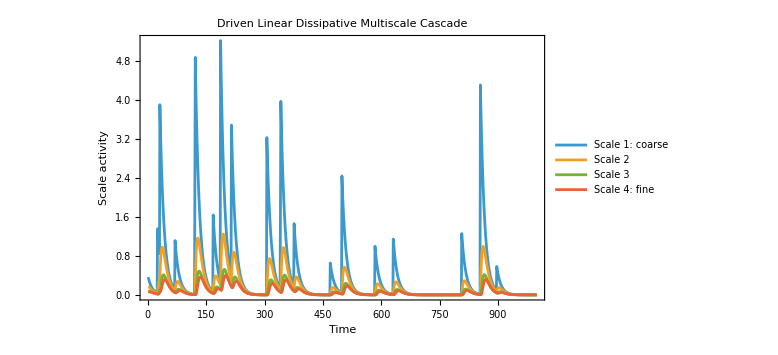

```mathematica
(*Visualisation for linear dissipative cascades*)
linearDissipativeScalePlot=ListLinePlot[Transpose[Take[linearDissipativeCascadeCore["ScaleStates"],1000]],PlotLegends->{"Scale 1: coarse","Scale 2","Scale 3","Scale 4: fine"},PlotRange->All,Frame->True,FrameLabel->{"Time","Scale activity"},PlotLabel->"Driven Linear Dissipative Multiscale Cascade",ImageSize->Large];
linearDissipativeScalePlot
```

```mathematica
(*Now adding non linear multiscale cascade*)
ClearAll[AddDrivenNonlinearMultiscaleCascade,nonlinearCascadeCore,nonlinearCascadeMarketBase,nonlinearCascadeResult,nonlinearCascadeStatePlot,nonlinearCascadeFluxPlot,nonlinearCascadeComparisonPlot];
Options[AddDrivenNonlinearMultiscaleCascade]={"MaximumTransferFractions"->{0.25,0.40,0.55},"TransferThresholds"->{0.35,0.14,0.06},"DissipationRates"->{0.01,0.03,0.08,0.45},"ObservationWeights"->{0.10,0.15,0.25,0.50},"FineDissipationWeight"->2.,"ActivityReference"->0.15,"ActivityCoupling"->3.};
AddDrivenNonlinearMultiscaleCascade[linearCore_Association,OptionsPattern[]]:=Module[{maximumTransferFractions,transferThresholds,dissipationRates,observationWeights,fineDissipationWeight,activityReference,activityCoupling,numberOfScales,coarseForcing,gaussianSource,initialState,nonlinearFlux,cascadeStep,statePath,scaleStates,transferFluxes,dissipationFluxes,fineScaleDissipation,weightedScaleEnergy,cascadeActivity,boundedCascadeActivity,relativeActivityScale,nonlinearSignal,baseParameters},maximumTransferFractions=N@OptionValue["MaximumTransferFractions"];
transferThresholds=N@OptionValue["TransferThresholds"];
dissipationRates=N@OptionValue["DissipationRates"];
observationWeights=N@OptionValue["ObservationWeights"];
fineDissipationWeight=N@OptionValue["FineDissipationWeight"];
activityReference=N@OptionValue["ActivityReference"];
activityCoupling=N@OptionValue["ActivityCoupling"];
numberOfScales=Length[dissipationRates];
If[Length[maximumTransferFractions]!=numberOfScales-1||Length[transferThresholds]!=numberOfScales-1||Length[observationWeights]!=numberOfScales,Return[Failure["InvalidCascadeDimensions",<|"Message"->"Transfer fractions and thresholds must have one fewer element than the number of scales."|>]]];
If[!AllTrue[transferThresholds,#>0.&],Return[Failure["InvalidTransferThreshold",<|"Message"->"Every transfer threshold must be positive."|>]]];
If[!AllTrue[Join[maximumTransferFractions,dissipationRates],#>=0.&],Return[Failure["NegativeRate",<|"Message"->"Transfer fractions and dissipation rates must be non-negative."|>]]];
If[!AllTrue[MapThread[Plus,{dissipationRates,Append[maximumTransferFractions,0.]}],#<=1.&],Return[Failure["InvalidActivityBudget",<|"Message"->"Maximum transfer plus dissipation cannot exceed one at any scale."|>]]];
If[Total[observationWeights]<=0.||activityReference<=0.,Return[Failure["InvalidObservationMap",<|"Message"->"Observation weights and ActivityReference must be positive."|>]]];
observationWeights=observationWeights/Total[observationWeights];
coarseForcing=linearCore["PeakImpulse"];
gaussianSource=linearCore["GaussianSource"];
initialState=ConstantArray[0.,numberOfScales];
(*At low energy:flux is approximately proportional to E^(3/2) At high energy:flux approaches maximumFraction E Therefore,outgoing flux is nonlinear but bounded.*)nonlinearFlux=Function[state,MapThread[Function[{energy,maximumFraction,threshold},maximumFraction energy*(Sqrt[energy/threshold]/(1.+Sqrt[energy/threshold]))],{Most[state],maximumTransferFractions,transferThresholds}]];
cascadeStep=Function[{state,forcing},Module[{outgoingFlux,dissipation,nextState},outgoingFlux=nonlinearFlux[state];
dissipation=dissipationRates state;
nextState=state-dissipation-Append[outgoingFlux,0.]+Prepend[outgoingFlux,0.];
nextState[[1]]+=forcing;
Map[Max[0.,#]&,nextState]]];
statePath=FoldList[cascadeStep,initialState,coarseForcing];
scaleStates=Rest[statePath];
transferFluxes=nonlinearFlux/@scaleStates;
dissipationFluxes=Map[dissipationRates #&,scaleStates];
fineScaleDissipation=dissipationFluxes[[All,-1]];
weightedScaleEnergy=scaleStates.observationWeights;
cascadeActivity=weightedScaleEnergy+fineDissipationWeight fineScaleDissipation;
boundedCascadeActivity=cascadeActivity/(activityReference+cascadeActivity);
relativeActivityScale=1.+activityCoupling boundedCascadeActivity;
nonlinearSignal=relativeActivityScale gaussianSource;
baseParameters=KeyDrop[linearCore["Parameters"],{"TransferRates","StationaryMeanScaleState","StationaryMeanCascadeActivity","StationaryVarianceCascadeActivity","VarianceNormalization","TheoreticalSignalVariance"}];
Join[KeyDrop[linearCore,{"ScaleStates","TransferFluxes","DissipationFluxes","CascadeActivity","ConditionalScale","Signal","Activity"}],<|"Model"->"OneDimensionalTurbulence","Stage"->"DrivenNonlinearMultiscaleCascade","Version"->"0.6","ParentStage"->"DrivenLinearDissipativeCascade","ForcingType"->"ExternallyDriven","TransferType"->"BoundedNonlinearE3Over2","DissipationType"->"LinearScaleDependent","Signal"->nonlinearSignal,"Activity"->nonlinearSignal^2,(*Same interface as the linear cascade*)"ScaleStates"->scaleStates,"TransferFluxes"->transferFluxes,"DissipationFluxes"->dissipationFluxes,"CascadeActivity"->cascadeActivity,"ConditionalScale"->relativeActivityScale,(*Additional nonlinear diagnostics*)"FineScaleDissipation"->fineScaleDissipation,"BoundedCascadeActivity"->boundedCascadeActivity,"Parameters"->Join[baseParameters,<|"NumberOfScales"->numberOfScales,"MaximumTransferFractions"->maximumTransferFractions,"TransferThresholds"->transferThresholds,"DissipationRates"->dissipationRates,"ObservationWeights"->observationWeights,"FineDissipationWeight"->fineDissipationWeight,"ActivityReference"->activityReference,"ActivityCoupling"->activityCoupling,"SignalVarianceNormalization"->"None"|>]|>]];
nonlinearCascadeCore=AddDrivenNonlinearMultiscaleCascade[linearDissipativeCascadeCore,"MaximumTransferFractions"->{0.25,0.40,0.55},"TransferThresholds"->{0.35,0.14,0.06},"DissipationRates"->{0.01,0.03,0.08,0.45},"ObservationWeights"->{0.10,0.15,0.25,0.50},"FineDissipationWeight"->2.,"ActivityReference"->0.15,"ActivityCoupling"->3.];
Head[nonlinearCascadeCore]
```

Association

```mathematica
(*Market adapter for non linear multiscale cascade*)
nonlinearCascadeMarketBase=GaussianMarketAdapter[nonlinearCascadeCore,"InitialPrice"->100.,"AnnualizedVolatility"->0.20];
nonlinearCascadeRelativeScale=nonlinearCascadeCore["ConditionalScale"];
nonlinearCascadePeriodScale=nonlinearCascadeMarketBase["MarketParameters"]["PeriodScale"];
nonlinearCascadeResult=Join[nonlinearCascadeMarketBase,<|"Volatility"->nonlinearCascadePeriodScale*nonlinearCascadeRelativeScale,"RelativeVolatility"->nonlinearCascadeRelativeScale|>];
```

-Graphics-

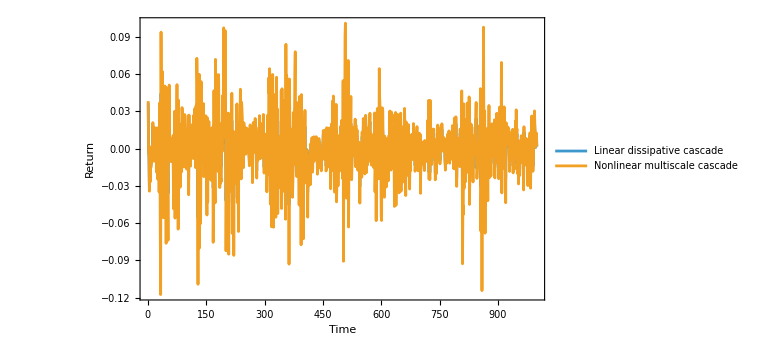

```mathematica
(*Plots for non linear multiscale cascade*)
nonlinearCascadeStatePlot=ListLinePlot[Transpose[Take[nonlinearCascadeCore["ScaleStates"],1000]],PlotLegends->{"Scale 1: coarse","Scale 2","Scale 3","Scale 4: fine"},PlotRange->All,Frame->True,FrameLabel->{"Time","Scale activity"},PlotLabel->"Nonlinear Multiscale States",ImageSize->Large];
nonlinearCascadeFluxPlot=ListLinePlot[Transpose[Take[nonlinearCascadeCore["TransferFluxes"],1000]],PlotLegends->{"Flux 1 -> 2","Flux 2 -> 3","Flux 3 -> 4"},PlotRange->All,Frame->True,FrameLabel->{"Time","Nonlinear transfer flux"},PlotLabel->"State-Dependent Interscale Transfer",ImageSize->Large];
GraphicsColumn[{nonlinearCascadeStatePlot,nonlinearCascadeFluxPlot}]
nonlinearCascadeComparisonPlot=ListLinePlot[{Take[linearDissipativeCascadeResult["Returns"],1000],Take[nonlinearCascadeResult["Returns"],1000]},PlotLegends->{"Linear dissipative cascade","Nonlinear multiscale cascade"},PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},ImageSize->Large];
nonlinearCascadeComparisonPlot
```

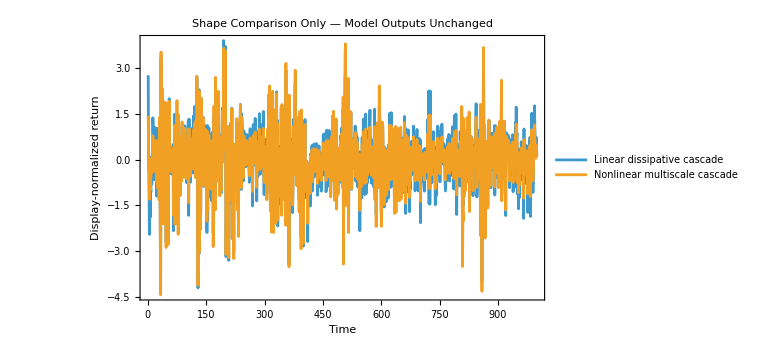

```mathematica
(*Normalized graph*)
linearDisplayReturns=linearDissipativeCascadeResult["Returns"]/Sqrt[Mean[linearDissipativeCascadeResult["Returns"]^2]];
nonlinearDisplayReturns=nonlinearCascadeResult["Returns"]/Sqrt[Mean[nonlinearCascadeResult["Returns"]^2]];
nonlinearCascadeShapeComparisonPlot=ListLinePlot[{Take[linearDisplayReturns,1000],Take[nonlinearDisplayReturns,1000]},PlotLegends->{"Linear dissipative cascade","Nonlinear multiscale cascade"},PlotRange->All,Frame->True,FrameLabel->{"Time","Display-normalized return"},PlotLabel->"Shape Comparison Only — Model Outputs Unchanged",ImageSize->Large];
nonlinearCascadeShapeComparisonPlot
```

```mathematica
currentValidationBundle=Module[{core,result,parameters,returns,prices,conditionalScale,periodsPerYear,observations,baseDirectory,timeStamp,exportDirectory,graphDirectory,verificationDirectory,sampleACF,structureMoment,nonlinearFlux,standardizedReturns,skewness,excessKurtosis,jarqueBeraStatistic,jarqueBeraPValue,tailProbabilities,tailComparison,rawReturnACF,absoluteReturnACF,squaredReturnACF,acfLags,aggregationHorizons,aggregationResults,structureLags,structureOrders,logPath,scalingResults,zetaValues,zetaCoefficients,zetaCurvature,scaleStates,transferFluxes,dissipationFluxes,previousStates,predictedStates,maximumTransferFractions,transferThresholds,dissipationRates,coarseForcing,budgetResidual,rebuiltCore,reproductionError,distributionSummary,internalDynamicsSummary,verificationSummary,pricePlot,returnsVolatilityPlot,distributionPlot,quantilePlot,acfPlot,aggregationPlot,scalingPlot,notebookPlots,currentPlots,verificationPlots,plotExportFiles,verificationPlotFiles,seriesTable,metadata,generatorFile,exportedFiles,hashFiles,sha256,report},core=nonlinearCascadeCore;
result=nonlinearCascadeResult;
parameters=core["Parameters"];
returns=N@result["Returns"];
prices=N@result["Prices"];
conditionalScale=N@core["ConditionalScale"];
periodsPerYear=result["MarketParameters"]["PeriodsPerYear"];
observations=Length[returns];
(*----------Export directory----------*)baseDirectory=Quiet@Check[NotebookDirectory[],$Failed];
If[!StringQ[baseDirectory],baseDirectory=Directory[]];
timeStamp=DateString[{"Year","Month","Day","-","Hour","Minute","Second"}];
exportDirectory=FileNameJoin[{baseDirectory,"exports","nonlinear-cascade-"<>timeStamp}];
graphDirectory=FileNameJoin[{exportDirectory,"graphs"}];
verificationDirectory=FileNameJoin[{exportDirectory,"verification"}];
CreateDirectory[graphDirectory,CreateIntermediateDirectories->True];
CreateDirectory[verificationDirectory,CreateIntermediateDirectories->True];
(*----------Helper functions----------*)sampleACF[data_List,maximumLag_Integer]:=Table[Correlation[Take[data,Length[data]-lag],Drop[data,lag]],{lag,1,maximumLag}];
structureMoment[path_List,lag_Integer,order_?NumericQ]:=Mean[Abs[Drop[path,lag]-Take[path,Length[path]-lag]]^order];
nonlinearFlux[state_List]:=MapThread[Function[{energy,maximumFraction,threshold},maximumFraction energy*(Sqrt[energy/threshold]/(1.+Sqrt[energy/threshold]))],{Most[state],maximumTransferFractions,transferThresholds}];
(*----------Distribution----------*)standardizedReturns=(returns-Mean[returns])/StandardDeviation[returns];
skewness=Skewness[returns];
excessKurtosis=Kurtosis[returns]-3.;
jarqueBeraStatistic=observations/6.*(skewness^2+excessKurtosis^2/4.);
jarqueBeraPValue=1.-CDF[ChiSquareDistribution[2],jarqueBeraStatistic];
distributionSummary=<|"Observations"->observations,"MeanReturn"->Mean[returns],"StandardDeviation"->StandardDeviation[returns],"AnnualizedVolatility"->Sqrt[periodsPerYear] StandardDeviation[returns],"Skewness"->skewness,"ExcessKurtosis"->excessKurtosis,"JarqueBeraStatistic"->jarqueBeraStatistic,"JarqueBeraPValue"->jarqueBeraPValue|>;
(*----------Tail comparison----------*)tailProbabilities={0.001,0.01,0.05,0.50,0.95,0.99,0.999};
tailComparison=Map[Function[probability,<|"Probability"->probability,"GeneratedQuantile"->Quantile[standardizedReturns,probability],"GaussianQuantile"->Quantile[NormalDistribution[0.,1.],probability]|>],tailProbabilities];
(*----------Autocorrelations----------*)acfLags=Range[20];
rawReturnACF=sampleACF[returns,20];
absoluteReturnACF=sampleACF[Abs[returns],20];
squaredReturnACF=sampleACF[returns^2,20];
(*----------Temporal aggregation----------*)aggregationHorizons={1,2,5,10,20,60,120};
aggregationResults=Map[Function[horizon,Module[{aggregatedReturns},aggregatedReturns=Total/@Partition[returns,horizon,horizon];
<|"Horizon"->horizon,"Observations"->Length[aggregatedReturns],"Skewness"->Skewness[aggregatedReturns],"ExcessKurtosis"->Kurtosis[aggregatedReturns]-3.|>]],aggregationHorizons];
(*----------Structure functions----------*)structureLags={1,2,4,8,16,32,64,128};
structureOrders=Range[0.5,5.,0.5];
logPath=Prepend[Accumulate[returns],0.];
scalingResults=Map[Function[order,Module[{moments,xValues,yValues,designMatrix,coefficients,predictedValues,totalVariation,residualVariation,rSquared},moments=Map[structureMoment[logPath,#,order]&,structureLags];
xValues=Log[N@structureLags];
yValues=Log[moments];
designMatrix=Transpose[{ConstantArray[1.,Length[xValues]],xValues}];
coefficients=LeastSquares[designMatrix,yValues];
predictedValues=designMatrix.coefficients;
totalVariation=Total[(yValues-Mean[yValues])^2];
residualVariation=Total[(yValues-predictedValues)^2];
rSquared=If[totalVariation==0.,1.,1.-residualVariation/totalVariation];
<|"Order"->order,"Zeta"->coefficients[[2]],"RSquared"->rSquared|>]],structureOrders];
zetaValues=Lookup[scalingResults,"Zeta"];
(*Fit:zeta(q)=a q+b q^2 without an intercept.*)zetaCoefficients=LeastSquares[Transpose[{structureOrders,structureOrders^2}],zetaValues];
zetaCurvature=zetaCoefficients[[2]];
(*----------Internal cascade validation----------*)scaleStates=N@core["ScaleStates"];
transferFluxes=N@core["TransferFluxes"];
dissipationFluxes=N@core["DissipationFluxes"];
maximumTransferFractions=parameters["MaximumTransferFractions"];
transferThresholds=parameters["TransferThresholds"];
dissipationRates=parameters["DissipationRates"];
coarseForcing=N@core["PeakImpulse"];
previousStates=Prepend[Most[scaleStates],ConstantArray[0.,Length[First[scaleStates]]]];
predictedStates=MapThread[Function[{previousState,forcing},Module[{outgoingFlux,dissipation,nextState},outgoingFlux=nonlinearFlux[previousState];
dissipation=dissipationRates previousState;
nextState=previousState-dissipation-Append[outgoingFlux,0.]+Prepend[outgoingFlux,0.];
nextState[[1]]+=forcing;
Map[Max[0.,#]&,nextState]]],{previousStates,coarseForcing}];
budgetResidual=Max[Abs[Flatten[scaleStates-predictedStates]]];
(*----------Deterministic regeneration----------*)rebuiltCore=AddDrivenNonlinearMultiscaleCascade[linearDissipativeCascadeCore,"MaximumTransferFractions"->parameters["MaximumTransferFractions"],"TransferThresholds"->parameters["TransferThresholds"],"DissipationRates"->parameters["DissipationRates"],"ObservationWeights"->parameters["ObservationWeights"],"FineDissipationWeight"->parameters["FineDissipationWeight"],"ActivityReference"->parameters["ActivityReference"],"ActivityCoupling"->parameters["ActivityCoupling"]];
reproductionError=Max[Abs[rebuiltCore["Signal"]-core["Signal"]]];
internalDynamicsSummary=<|"Stage"->core["Stage"],"Version"->core["Version"],"NumberOfScales"->Length[First[scaleStates]],"ScaleStateDimensions"->Dimensions[scaleStates],"TransferFluxDimensions"->Dimensions[transferFluxes],"MinimumScaleState"->Min[Flatten[scaleStates]],"MinimumTransferFlux"->Min[Flatten[transferFluxes]],"MinimumDissipationFlux"->Min[Flatten[dissipationFluxes]],"MaximumBudgetResidual"->budgetResidual,"ExactDeterministicRegeneration"->SameQ[rebuiltCore["Signal"],core["Signal"]],"MaximumRegenerationError"->reproductionError,"ExpectedPeakFrequency"->parameters["PeakProbability"],"RealizedPeakFrequency"->Mean[core["PeakIndicator"]],"MeanConditionalScale"->Mean[conditionalScale],"MaximumConditionalScale"->Max[conditionalScale],"MeanFineScaleDissipation"->Mean[core["FineScaleDissipation"]],"MaximumFineScaleDissipation"->Max[core["FineScaleDissipation"]]|>;
verificationSummary=<|"Distribution"->distributionSummary,"TailComparison"->tailComparison,"RawReturnACFFirst20Lags"->rawReturnACF,"AbsoluteReturnACFFirst20Lags"->absoluteReturnACF,"SquaredReturnACFFirst20Lags"->squaredReturnACF,"MaximumAbsoluteRawReturnACFFirst20Lags"->Max[Abs[rawReturnACF]],"MeanAbsoluteReturnACFFirst20Lags"->Mean[Abs[absoluteReturnACF]],"MeanSquaredReturnACFFirst20Lags"->Mean[Abs[squaredReturnACF]],"ApproximateSingleLag95PercentBand"->1.96/Sqrt[observations],"Aggregation"->aggregationResults,"ScalingExponents"->scalingResults,"ZetaLinearCoefficient"->zetaCoefficients[[1]],"ZetaCurvature"->zetaCurvature,"InternalDynamics"->internalDynamicsSummary|>;
(*----------Primary output plots----------*)pricePlot=ListLinePlot[prices,PlotRange->All,Frame->True,FrameLabel->{"Time","Synthetic price"},PlotLabel->"Nonlinear Cascade Market Path",ImageSize->Large];
returnsVolatilityPlot=GraphicsColumn[{ListLinePlot[returns,PlotRange->All,Frame->True,FrameLabel->{"Time","Return"},PlotLabel->"Generated Returns",ImageSize->Large],ListLinePlot[result["Volatility"],PlotRange->All,Frame->True,FrameLabel->{"Time","Conditional scale"},PlotLabel->"Derived Market Volatility",ImageSize->Large]}];
(*----------Verification plots----------*)distributionPlot=Show[Histogram[standardizedReturns,60,"PDF",ChartStyle->Directive[Opacity[0.55],RGBColor[0.2,0.55,0.8]],Frame->True,FrameLabel->{"Standardized return","Density"}],Plot[PDF[NormalDistribution[0.,1.],x],{x,-6.,6.},PlotStyle->{Red,Thick}],PlotRange->{{-6.,6.},All},PlotLabel->"Generated Distribution versus Gaussian",ImageSize->Large];
quantilePlot=Module[{probabilities,generatedQuantiles,gaussianQuantiles},probabilities=Range[0.001,0.999,0.001];
generatedQuantiles=Quantile[standardizedReturns,probabilities];
gaussianQuantiles=Quantile[NormalDistribution[0.,1.],probabilities];
ListPlot[Transpose[{gaussianQuantiles,generatedQuantiles}],PlotStyle->Directive[PointSize[0.004],RGBColor[0.2,0.55,0.8]],Frame->True,FrameLabel->{"Gaussian quantile","Generated quantile"},PlotLabel->"Gaussian Q-Q Plot",Epilog->{Red,Dashed,Line[{{-5.,-5.},{5.,5.}}]},PlotRange->All,ImageSize->Large]];
acfPlot=ListLinePlot[{Transpose[{acfLags,rawReturnACF}],Transpose[{acfLags,absoluteReturnACF}],Transpose[{acfLags,squaredReturnACF}]},PlotLegends->{"Returns","Absolute returns","Squared returns"},Frame->True,FrameLabel->{"Lag","Autocorrelation"},PlotRange->All,PlotLabel->"Temporal Dependence",ImageSize->Large];
aggregationPlot=ListLinePlot[Transpose[{Lookup[aggregationResults,"Horizon"],Lookup[aggregationResults,"ExcessKurtosis"]}],PlotMarkers->Automatic,Frame->True,FrameLabel->{"Aggregation horizon","Excess kurtosis"},PlotLabel->"Tail Persistence under Aggregation",PlotRange->All,ImageSize->Large];
scalingPlot=ListLinePlot[{Transpose[{structureOrders,zetaValues}],Transpose[{structureOrders,structureOrders/2.}]},PlotLegends->{"Generated zeta(q)","Gaussian q/2"},PlotMarkers->Automatic,Frame->True,FrameLabel->{"Moment order q","Scaling exponent zeta(q)"},PlotLabel->"Structure-Function Scaling",PlotRange->All,ImageSize->Large];
(*----------Collect existing notebook plots----------*)notebookPlots=Select[<|"01-gaussian-vs-peak-frequency"->If[ValueQ[peakFrequencyComparisonPlot],peakFrequencyComparisonPlot,Missing["NotAvailable"]],"02-fixed-vs-distributed-severity"->If[ValueQ[peakSeverityComparisonPlot],peakSeverityComparisonPlot,Missing["NotAvailable"]],"03-persistent-episode-returns"->If[ValueQ[persistentClusterReturnPlot],persistentClusterReturnPlot,Missing["NotAvailable"]],"04-persistent-episode-activity"->If[ValueQ[persistentClusterActivityPlot],persistentClusterActivityPlot,Missing["NotAvailable"]],"05-linear-dissipative-scale-states"->If[ValueQ[linearDissipativeScalePlot],linearDissipativeScalePlot,Missing["NotAvailable"]],"06-nonlinear-scale-states"->If[ValueQ[nonlinearCascadeStatePlot],nonlinearCascadeStatePlot,Missing["NotAvailable"]],"07-nonlinear-transfer-fluxes"->If[ValueQ[nonlinearCascadeFluxPlot],nonlinearCascadeFluxPlot,Missing["NotAvailable"]],"08-linear-vs-nonlinear-output"->If[ValueQ[nonlinearCascadeComparisonPlot],nonlinearCascadeComparisonPlot,Missing["NotAvailable"]],"09-display-normalized-comparison"->If[ValueQ[nonlinearCascadeShapeComparisonPlot],nonlinearCascadeShapeComparisonPlot,Missing["NotAvailable"]]|>,Not@MissingQ[#]&];
currentPlots=Join[notebookPlots,<|"10-current-price-path"->pricePlot,"11-current-returns-volatility"->returnsVolatilityPlot|>];
verificationPlots=<|"01-distribution"->distributionPlot,"02-qq-plot"->quantilePlot,"03-autocorrelations"->acfPlot,"04-aggregation"->aggregationPlot,"05-scaling-exponents"->scalingPlot|>;
(*----------Export plots----------*)plotExportFiles=Association@KeyValueMap[Function[{name,plot},Export[FileNameJoin[{graphDirectory,name<>".png"}],plot,ImageResolution->200];
Export[FileNameJoin[{graphDirectory,name<>".pdf"}],plot];
name->FileNameJoin[{graphDirectory,name<>".png"}]],currentPlots];
verificationPlotFiles=Association@KeyValueMap[Function[{name,plot},Export[FileNameJoin[{verificationDirectory,name<>".png"}],plot,ImageResolution->200];
Export[FileNameJoin[{verificationDirectory,name<>".pdf"}],plot];
name->FileNameJoin[{verificationDirectory,name<>".png"}]],verificationPlots];
Export[FileNameJoin[{exportDirectory,"results.pdf"}],Values[currentPlots]];
Export[FileNameJoin[{exportDirectory,"statistical-verification.pdf"}],Values[verificationPlots]];
(*----------Export model data----------*)seriesTable=Prepend[MapThread[List,{Range[observations],returns,prices,conditionalScale,core["CascadeActivity"],core["FineScaleDissipation"]}],{"Time","Return","Price","RelativeConditionalScale","CascadeActivity","FineScaleDissipation"}];
Export[FileNameJoin[{exportDirectory,"market-series.csv"}],seriesTable,"CSV"];
Export[FileNameJoin[{exportDirectory,"market-result.wxf"}],result,"WXF"];
Export[FileNameJoin[{exportDirectory,"nonlinear-cascade-core.wxf"}],core,"WXF"];
Export[FileNameJoin[{exportDirectory,"statistical-verification.wxf"}],verificationSummary,"WXF"];
Export[FileNameJoin[{exportDirectory,"summary.json"}],verificationSummary,"RawJSON"];
metadata=<|"CreatedAt"->DateString["ISODateTime"],"Model"->core["Model"],"Stage"->core["Stage"],"Version"->core["Version"],"Observations"->observations,"PeriodsPerYear"->periodsPerYear,"Parameters"->parameters|>;
Export[FileNameJoin[{exportDirectory,"metadata.json"}],metadata,"RawJSON"];
(*----------Export generator definitions----------*)generatorFile=FileNameJoin[{exportDirectory,"generator-definition.wl"}];
Save[generatorFile,{GenerateGaussianCore,GaussianMarketAdapter,AddIndependentPeakFrequency,AddPeakSeverityDistribution,AddPersistentPeakEpisodes,AddDrivenLinearDissipativeCascade,AddDrivenNonlinearMultiscaleCascade}];
(*----------SHA-256 integrity manifest----------*)hashFiles=Select[FileNames["*",exportDirectory,Infinity],FileType[#]===File&];
sha256=Association@Map[Function[file,FileNameTake[file]->IntegerString[FileHash[file,"SHA256"],16,64]],hashFiles];
Export[FileNameJoin[{exportDirectory,"sha256.json"}],sha256,"RawJSON"];
exportedFiles=FileNames["*",exportDirectory,Infinity];
report=<|"ExportDirectory"->exportDirectory,"ExportedNotebookPlots"->Keys[currentPlots],"ExportedVerificationPlots"->Keys[verificationPlots],"VerificationSummary"->verificationSummary,"Files"->exportedFiles|>;
report];

Dataset[<|"ExportDirectory"->currentValidationBundle["ExportDirectory"],"FilesExported"->Length[currentValidationBundle["Files"]],"Observations"->currentValidationBundle["VerificationSummary"]["Distribution"]["Observations"],"AnnualizedVolatility"->currentValidationBundle["VerificationSummary"]["Distribution"]["AnnualizedVolatility"],"ExcessKurtosis"->currentValidationBundle["VerificationSummary"]["Distribution"]["ExcessKurtosis"],"ZetaCurvature"->currentValidationBundle["VerificationSummary"]["ZetaCurvature"],"MaximumBudgetResidual"->currentValidationBundle["VerificationSummary"]["InternalDynamics"]["MaximumBudgetResidual"],"ExactRegeneration"->currentValidationBundle["VerificationSummary"]["InternalDynamics"]["ExactDeterministicRegeneration"]|>]
```

General::munfl: Exp[-1050.46] is too small to represent as a normalized machine number; precision may be lost.